# Краен изпит на Светослав Добромиров Славов, Фак. №2001261051

## Задача 1.

```mathematica
f[x_] := (50(5+2)Sin[x]+x^3+33)/((1+2)+x^2)
```

```mathematica
f[x]
```

(33+x^3+350 Sin[x])/(3+x^2)

### а) Да се намери броят на корените на уравнението

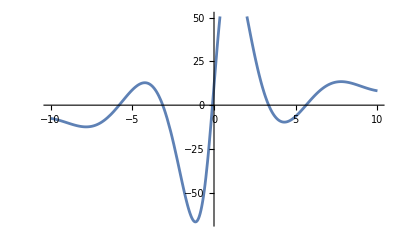

```mathematica
Plot[f[x], {x, -10, 10}]
```

Общ брой на корените: 5

### б) Да се локализира най-малкият реален корен в интервал [p, q]

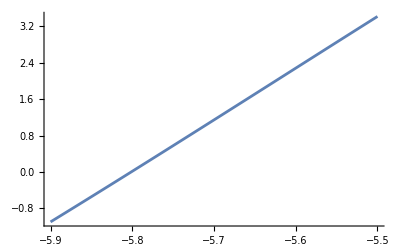

```mathematica
Plot[f[x], {x, -5.9, -5.5}]
```

```mathematica
f[-5.9]
```

-1.09818

```mathematica
f[-5.5]
```

3.41546

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус).
(2) f(-5.9) = -1.09818 > 0 и f(-5.5) = 3.41546 < 0
=> Функцията има различни знаци в двата края на разглеждания интервал [-5.9; -5.5].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [-5.9; -5.5].

### в) Да се проверят условията за метода на хордите

#### Проверка на сходимост:

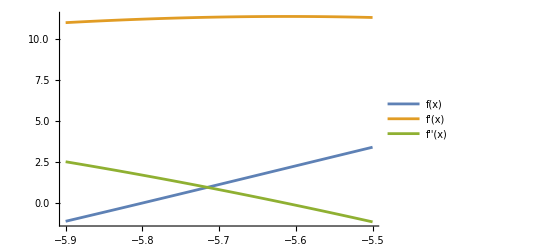

```mathematica
Plot[{f[x],f'[x], f''[x]}, {x,-5.9, -5.5}, PlotLegends->"Expressions"]
```

#### Графика на първата производна

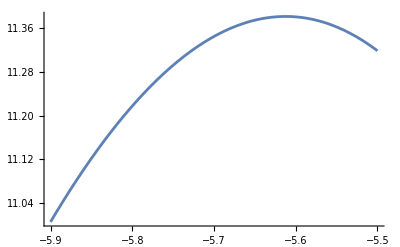

```mathematica
Plot[f'[x],{x,-5.9,-5.5}]
```

Извод: (1) Стойностите на първата производна в разглеждания интервал [-5.9; -5.5] са между 11 и 11.4. Следователно първата f'(x) > 0 в целия разглеждан интервал [-5.9; -5.5].

#### Графика на втората производна

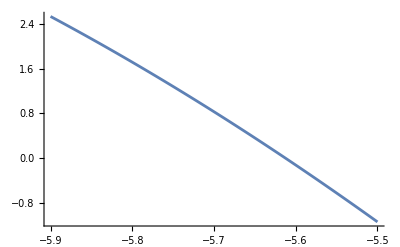

```mathematica
Plot[f''[x],{x,-5.9,-5.5}]
```

Извод : (2) Стойностите на втората производна в разглеждания интервал [-5.9; -5.5] са между 2 и - 1. Следователно втората f'' (x) > 0 в целия разглеждан интервал [-5.9; -5.5].

Извод: От (1) и (2) следва, че първата и втората производна имат постоянни знаци в разглеждания интервал [-5.9; -5.5]. Следователно условията за сходимост на метода на хордите са изпълнени.

### г) Да се определи началното приближение и постоянната точка за метода на хордите

Избор на начално приближение и постоянна точка
Нужно е да е изпълнено условието f(x0).f’’(x) < 0
В нашия случай f’’(x) < 0. Следователно е нужно f(x0) > 0

```mathematica
f[-5.9]
```

-1.09818

```mathematica
f[-5.5]
```

3.41546

```mathematica
p = -5.5
```

-5.5

```mathematica
x0 = -5.9
```

-5.9

### д) Колко итерации са необходими за достигане на точност 10^-3?

#### Изчисляване на постоянните величини

```mathematica
Plot[Abs[f'[x]],{x,-5.9,-5.5}]
```

-Graphics-

От геометрично съображение минимумът на абсолютната стойност на първата производна се достига в левия край на интервала, а максимумът - в десния.

```mathematica
M1 = Abs[f'[-5.9]]
```

11.0047

```mathematica
m1 = Abs[f'[-5.5]]
```

11.3189

```mathematica
R = (M1 - m1)/m1
```

-0.0277588

#### Итериране

```mathematica
M1 = Abs[f'[-2.5]];
m1 = Abs[f'[-3.5]];
R = (M1 - m1)/m1;
f[x_] := -2 x^3 -47Cos[x] - 70
p = -2.5; x0 = -3.5;
epszad = 0.00001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x_n) = ", N[f[x0]]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/(f[x0] - f[p])*(x0 - p);
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1], " ε_n = ", eps = R * Abs[x1 - x0]];
x0 = x1
]
```

n = 0 x_n = -3.5 f(x_n) = 59.7635

n = 1 x_n = -2.51801 f(x_n) = 0.0846361 ε_n = 1.4918

n = 2 x_n = -2.51672 f(x_n) = 0.0000845987 ε_n = 0.00196125

n = 3 x_n = -2.51672 f(x_n) = 8.44756×10^-8 ε_n = 1.96023×10^-6

Извод: 2 итерации са ни необходими

### е) Да се провери колко итерации биха били необходими, ако се използва методът на разполовяването в същия интервал [p, q] за същата точност.

```mathematica
Log2[(-5.9 +5.5)/0.001] - 1
```

7.64386+4.53236 ⅈ

### ж) Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на разполовяването биха били необходими имагинерно много итерации за достигане на исканата точност. А по метода на хордите бяха необходими 2 итерации. Следователно методът на хордите е по-ефективен за избрания интервал [-5.9, -5.5].